# Agent Workflow

The  idea  of  the  workflow :

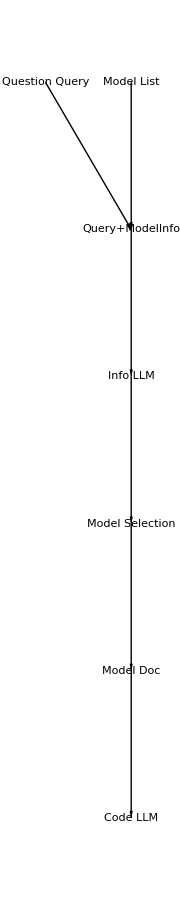

```mathematica
elist={{"Question Query"->"Query+ModelInfo","1st Chat"},{"Model List"->"Query+ModelInfo","model_list.md"},{"Query+ModelInfo"->"Info LLM","Prompt"},{"Model Selection"->"Model Doc","2nd Chat"},{"Model Doc"->"Code LLM","doc+query"},{"Info LLM"->"Model Selection","1st Respond"}};

GraphComputation`GraphPlotLegacy[elist,DirectedEdges->True,EdgeLabeling->True,VertexLabeling->True,ImageSize->500,BaseStyle->15,PlotStyle->Black,Method->"LayeredDigraphDrawing"]
```

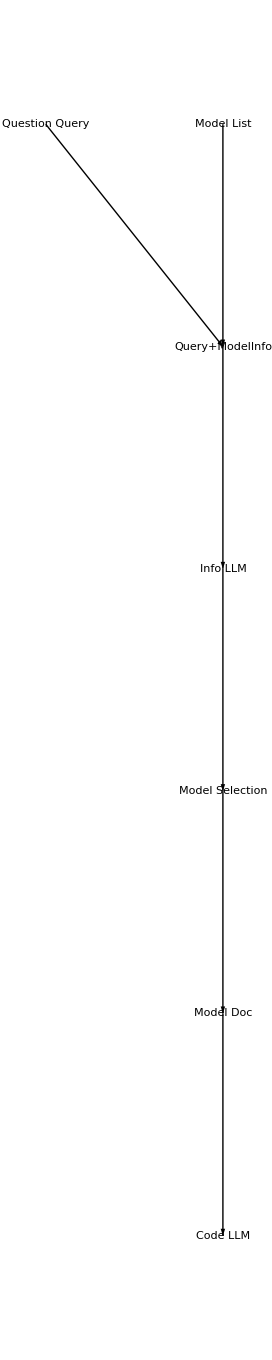

```mathematica
Show[%94,AspectRatio->Full]
```

## Initialize Chat History

```mathematica
chatHistory = {};
question = "My case is I have three groups of images about lamps that ready to classfied. So what i expect is when i give a new image it can tell me which group it belongs to";
prompt = StringTemplate["You are an expert on Machine Learning and Deep Learning. The main task is choose best model for Transfer Learning. Here the model_list.md is provided you have to read it first where contians ML models info. You will choose the 3 best fit models from the model_list for my case if there is not best fit for user request you need to find close one with explanation why you choose them. Your must explain why each model is good for transfer learning on user case. My request: `question`"][<|"question" -> question|>]
```

You are an expert on Machine Learning and Deep Learning. The main task is choose best model for Transfer Learning. Here the model_list.md is provided you have to read it first where contians ML models info. You will choose the 3 best fit models from the model_list for my case if there is not best fit for user request you need to find close one with explanation why you choose them. Your must explain why each model is good for transfer learning on user case. My request: My case is I have three groups of images about lamps that ready to classfied. So what i expect is when i give a new image it can tell me which group it belongs to

## Generate the First respond from LLM

```mathematica
conversation=LLMSynthesize[prompt,LLMEvaluator-> <|"Tools"->LLMResourceTool["ImportFile"][<|"MaxLength" -> 8000|>]|>]
```

Sure, I can assist you with selecting the appropriate machine learning models for your specific task. Let's first take a look at the model_list.md file to understand the available models and how they might fit your needs.

Based on the list of models, for your task of classifying various groups of images of lamps, you would need a model that can efficiently classify images. For this I would suggest, Convolutional Neural Networks (CNN) based models, as they are specifically designed for tasks like image classification.

Here are three models that would be particularly suited to your needs:

1. **Ademxapp Model A**: This one is a great choice because it's trained to identify the main object in an image. It is trained on the "ImageNet Competition Data" which is a large scale dataset used for Image classification. This would be beneficial for your task as it would be able to distinguish different types of lamps easily.

2. **CenterNet**: This model is used to detect and localize objects in an image. It's trained on "MS-COCO Data", another well-known dataset with various objects. Although it's primarily for object detection, it can also be used for simple classification tasks.

3. **DenseNet-121**: Although full details about this model were not provided in the list, DenseNet models are also used for image classification tasks and they can be very useful for your case.

These models are chosen because, in transfer learning, we leverage the knowledge gained from a previously trained model (like the ones mentioned here, which were trained with large scale datasets) and apply this knowledge to a new but similar problem (your images of lamps). Since these models have learned to identify and differentiate between numerous objects, they'd likely perform well when tasked with differentiating between various types of lamps.

```mathematica
(*Function for append the chat history into list*)
UpdataChatHistory[user_, agent_]:= AppendTo[chatHistory,{"user"->user, "agent"->agent}]
```

```mathematica
UpdataChatHistory[question, conversation];
```

```mathematica
chatHistory
```

{{user→My case is I have lots of images about lamps that ready to classfied.,agent→Let's first import the model_list.md file so that I can make the most informed decision on which 3 models will best fit your case.

Thanks for providing the model list. Based on your case of having lots of images of lamps for classification and the Machine Learning/Deep Learning models provided, here are the best 3 fit models:

1. **CenterNet** - This model has been trained on the "MS-COCO Data" set and it can detect and localize objects in an image. Given the task of classifying images of lamps, this model can be of great use to identify the location and the presence of a lamp in an image.

2. **Ademxapp Model A** - This model is used to identify the main object in an image and has been trained on the "ImageNet Competition Data" which is a large scale visual recognition challenge and encompasses many categories of objects, likely including various types of lamps.

3. **D2-Net** - This model finds generic keypoints and their feature vectors in an image. It has been trained on "MegaDepth Data" which can handle a large variety of scenes, transformations, and imaging conditions. It could help to identify unique features of different types of lamps.

While specific models for classifying different types of lamps weren't present in the list provided, the 3 models chosen should be capable of carrying out the task based on their ability to identify objects and keypoints in the image. You might need to retrain these models with your specific data set (pictures of various lamps) for optimal performance.}}

## Define a Retrieve History Funtion

```mathematica
(*Define a function to extract content based on the key*)ExtractChatContent[chatHistory_,key_]:=Module[{content},content=Cases[chatHistory,{___,key->value_,___}:>value];
content]
```

```mathematica
ExtractChatContent[chatHistory,"user"]
```

{My case is I have lots of images about lamps that ready to classfied.}

## Second Prompt for Model Selection

```mathematica
user1="Ademxapp Model A1 - ADE20K Data-trained version";
prompt2 = StringTemplate["OK i will choose this model: `model_name`. before we starting to implement, you need to introduce the model to me from follow aspects: - What kind of data input should i prepare, be specific and give me example? - Your plan of implement this model get ready to use with wolfram language."][<|"model_name" -> user1|>];
```

## Create a RAG system for Model Document

```mathematica
mdContent = Import["model_list.md"];
sections = StringSplit[mdContent,"---"];
processedSections=StringTrim/@sections;
Length[processedSections]
```

157

```mathematica
processedSections[[19]]
```

### Model Name
Name: "CLIP Multi-domain Feature Extractor"

### Description of the model
Represent words and images as vectors

### Trained by Data
DataSet: "N/A"

### Time issued
April 10, 2023

```mathematica
(*Get access to OpenAI's embedding model*)
embeddings = Map[ServiceExecute["OpenAI", "Embedding", {"Input" -> #, "Model" -> "text-embedding-3-small"}]&,processedSections]
```

```mathematica
embeddings[[All,"data",1,"embedding"]]//Length
```

157

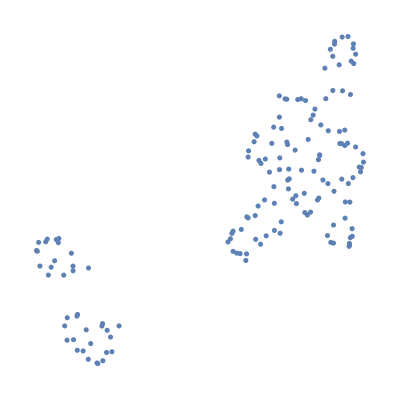

```mathematica
FeatureSpacePlot[
embeddings[[All,"data",1,"embedding"]],
Method->"UMAP"
]
```

```mathematica
embeddingsToText = MapThread[Rule[#1,#2]&,{embeddings[[All,"data",1,"embedding"]],processedSections}]
```

```mathematica
nfunction = Nearest[embeddingsToText, DistanceFunction->CosineDistance]
```

NearestFunction[{1536, <>}]

```mathematica
getEmbedding[text_String]:=
ServiceExecute[
"OpenAI",
"Embedding",
{
"Input" -> text, 
"Model" -> "text-embedding-3-small"
}
][["data",1,"embedding"]]
```

```mathematica
getEmbedding[user1]//Short
```

getEmbedding[user1]

```mathematica
user1
```

user1

```mathematica
getEmbedding["I want the images in sections"]
```

```mathematica
(*Function for calling retrieve info*)
nfunction[getEmbedding["CLIP image and text pair or descrption"],4]
```

{### Model Name
Name: "CLIP Multi-domain Feature Extractor"

### Description of the model
Represent words and images as vectors

### Trained by Data
DataSet: "N/A"

### Time issued
April 10, 2023,### Model Name
Name: "OpenCLIP Multi-domain Feature Extractor "

### Description of the model
Represent words and images as vectors

### Trained by Data
DataSet: "LAION-2B Data"

### Time issued
October 26, 2023,## Model List
## Model List

### Model Name
Name: "OpenCLIP Multi-domain Feature Extractor "

### Description of the model
Represent words and images as vectors

### Trained by Data
DataSet: "DataComp-1B Data"

### Time issued
October 26, 2023,### Model Name
Name: "CoCa Image Captioning Nets "

### Description of the model
Represent words and images as vectors

### Trained by Data
DataSet: "LAION-2B Data"

### Time issued
October 27, 2023}